# Last Names By First Letter in the U.S.

(I start off every notebook with these two commands to clear the namespace and anchor the directory)

```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
```

```mathematica
csv = Import["https://www2.census.gov/topics/genealogy/2010surnames/names.zip", "Names_2010Census.csv"];
```

Let’s see what we’re working with here

```mathematica
First@csv
Last@csv
```

{name,rank,count,prop100k,cum_prop100k,pctwhite,pctblack,pctapi,pctaian,pct2prace,pcthispanic}

{ALL OTHER NAMES,0,29312001,9936.97,9936.97,66.65,8.53,7.97,0.86,2.32,13.67}

We’ll need to eliminate that final row. But out of curiosity, what proportion of people are unaccounted for in the data?

```mathematica
population = Total[#[[3]]& /@ Rest@csv];
Print["Percent of population with obscure names: " <> ToString[100. * (Last@csv)[[3]] / population] <> "%"]
```

Percent of population with obscure names: 9.93697%

Get totals by first letter of last name for all the rows in between the first and last

```mathematica
data = #[[1;;3]]& /@ csv[[2;;-2]];
firstLetters = { #[[3]], StringTake[#[[1]], 1] }& /@ data;
byFirstLetter = KeySort[Total /@ GroupBy[firstLetters, Last -> First]]
```

<|A→10080086,B→22587641,C→20582563,D→12045696,E→4932313,F→8981809,G→14814448,H→18810320,I→1097235,J→7935401,K→8669408,L→13045257,M→25610240,N→5069517,O→4051850,P→13233868,Q→642349,R→15699799,S→25056728,T→9413187,U→617005,V→4657504,W→14741478,X→102201,Y→1684921,Z→1504404|>

And convert to percentages

```mathematica
total = Total@byFirstLetter;
percents = byFirstLetter / total * 1.0
```

<|A→0.0379425,B→0.0850223,C→0.077475,D→0.0453413,E→0.0185658,F→0.0338085,G→0.0557632,H→0.0708041,I→0.00413011,J→0.0298697,K→0.0326326,L→0.0491037,M→0.0963997,N→0.0190822,O→0.0152516,P→0.0498137,Q→0.00241787,R→0.0590957,S→0.0943162,T→0.0354322,U→0.00232247,V→0.0175313,W→0.0554885,X→0.000384696,Y→0.00634222,Z→0.00566274|>

Whenever in doubt, visualize!

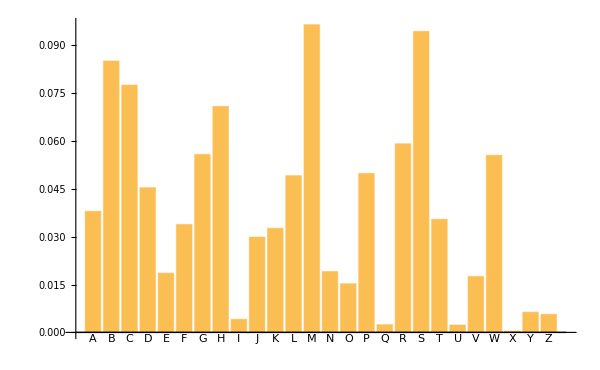

```mathematica
BarChart[percents, ChartLabels->Keys@percents, ImageSize->600]
```

```mathematica
Save["./data/last_name_percents.wl", percents];
```